```mathematica
<<ComputationalGeometry`
```

```mathematica
atlas=-Graphics-;
```

```mathematica
width = 1247;
height = 502;
points={{38.4707,304.151},{38.4707,243.697},{65.9498,203.394},{80.6053,159.428},{25.6471,194.234},{9.15969,232.705},{5.49581,265.68},{84.2691,322.47},{148.387,331.63},{185.026,294.991},{214.337,251.025},{194.185,342.621},{283.95,381.092},{415.85,414.067},{577.06,448.874},{727.279,492.84},{780.405,480.017},{789.565,461.697},{751.094,425.059},{707.128,388.42},{663.161,351.781},{632.019,393.916},{584.388,353.613},{507.447,331.63},{531.262,309.647},{633.85,331.63},{481.8,240.033},{483.632,316.974},{159.379,130.117},{218.001,152.1},{360.892,31.192},{227.16,163.092},{368.219,42.1836},{500.119,56.8391},{518.438,86.1501},{531.262,64.1669},{597.212,64.1669},{681.481,133.781},{741.935,135.612},{738.271,104.47},{840.859,27.5281},{904.977,38.5198},{1047.87,22.0323},{1108.32,49.5114},{1152.29,161.26},{1229.23,100.806},{1209.08,5.54488},{981.919,205.226},{937.952,236.369},{1093.67,232.705},{1113.82,276.672},{1077.18,331.63},{998.406,426.891},{897.649,491.008},{855.515,478.185},{853.683,458.033},{862.843,293.159},{818.876,456.202},{754.758,298.655},{654.002,232.705},{670.489,177.747},{747.431,186.907},{926.96,130.117},{1130.31,93.4779},{798.725,232.705},{505.615,185.075},{327.917,172.251},{327.917,265.68},{714.456,441.546},{677.817,395.748},{309.597,318.806},{566.069,410.403}};
normPoints = Map[({#[[1]] / width, #[[2]]/height})&,points];
```

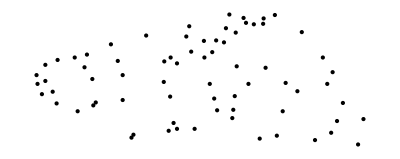

```mathematica
Graphics[Point[points]]
```

```mathematica
freq =5;
extraPoints = Join[
Table[{0,i},{i,0,1, 1/freq}],
Table[{1,i},{i,0,1, 1/freq}],
Table[{i,0},{i,0,1, 1/freq}],
Table[{i,1},{i,0,1, 1/freq}]
];
allPoints = Join[extraPoints, normPoints];
```

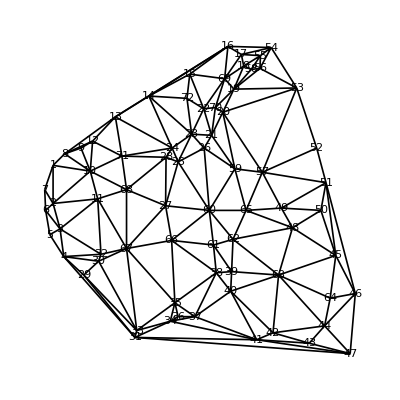

```mathematica
PlanarGraphPlot[normPoints]
```

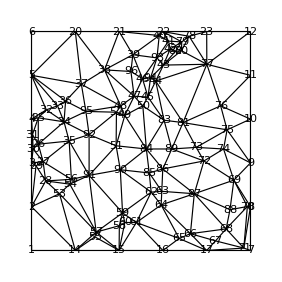

```mathematica
(* *)
PlanarGraphPlot[allPoints]
```

```mathematica
pointsToWarpXML[points_,triangulation_]:=(
header="<Warp>";
affineparams=StringJoin[
"<rotation>","0","</rotation>",
"<translationX>","0","</translationX>",
"<translationY>","0","</translationY>",
"<scaleX>","1","</scaleX>",
"<scaleY>","1","</scaleY>"
];
toFloatArrayXML[x_]:=StringJoin[Map[
(StringJoin[
"<float>",ToString[#],"</float>"
]
)&,
x
]];
affinemat=toFloatArrayXML[Flatten[IdentityMatrix[4]]];
src=StringJoin[
"<srcVertices>",toFloatArrayXML[Flatten[points]],"</srcVertices>"];
dst=StringJoin[
"<dstVertices>",toFloatArrayXML[Flatten[points]],"</dstVertices>"];
tri=StringJoin["<triangles>",toFloatArrayXML[triangulation],"</triangles>"];
footer="</Warp>";
StringJoin[{
header,affineparams,affinemat,src,dst,tri,footer
}]
);
```

```mathematica
pointsToWarpXML[points,{1}]
```

<Warp><rotation>0</rotation><translationX>0</translationX><translationY>0</translationY><scaleX>1</scaleX><scaleY>1</scaleY><float>1</float><float>0</float><float>0</float><float>0</float><float>0</float><float>1</float><float>0</float><float>0</float><float>0</float><float>0</float><float>1</float><float>0</float><float>0</float><float>0</float><float>0</float><float>1</float><srcVertices><float>38.4707</float><float>304.151</float><float>38.4707</float><float>243.697</float><float>65.9498</float><float>203.394</float><float>80.6053</float><float>159.428</float><float>25.6471</float><float>194.234</float><float>9.15969</float><float>232.705</float><float>5.49581</float><float>265.68</float><float>84.2691</float><float>322.47</float><float>148.387</float><float>331.63</float><float>185.026</float><float>294.991</float><float>214.337</float><float>251.025</float><float>194.185</float><float>342.621</float><float>283.95</float><float>381.092</float><float>415.85</float><float>414.067</float><float>577.06</float><float>448.874</float><float>727.279</float><float>492.84</float><float>780.405</float><float>480.017</float><float>789.565</float><float>461.697</float><float>751.094</float><float>425.059</float><float>707.128</float><float>388.42</float><float>663.161</float><float>351.781</float><float>632.019</float><float>393.916</float><float>584.388</float><float>353.613</float><float>507.447</float><float>331.63</float><float>531.262</float><float>309.647</float><float>633.85</float><float>331.63</float><float>481.8</float><float>240.033</float><float>483.632</float><float>316.974</float><float>159.379</float><float>130.117</float><float>218.001</float><float>152.1</float><float>360.892</float><float>31.192</float><float>227.16</float><float>163.092</float><float>368.219</float><float>42.1836</float><float>500.119</float><float>56.8391</float><float>518.438</float><float>86.1501</float><float>531.262</float><float>64.1669</float><float>597.212</float><float>64.1669</float><float>681.481</float><float>133.781</float><float>741.935</float><float>135.612</float><float>738.271</float><float>104.47</float><float>840.859</float><float>27.5281</float><float>904.977</float><float>38.5198</float><float>1047.87</float><float>22.0323</float><float>1108.32</float><float>49.5114</float><float>1152.29</float><float>161.26</float><float>1229.23</float><float>100.806</float><float>1209.08</float><float>5.54488</float><float>981.919</float><float>205.226</float><float>937.952</float><float>236.369</float><float>1093.67</float><float>232.705</float><float>1113.82</float><float>276.672</float><float>1077.18</float><float>331.63</float><float>998.406</float><float>426.891</float><float>897.649</float><float>491.008</float><float>855.515</float><float>478.185</float><float>853.683</float><float>458.033</float><float>862.843</float><float>293.159</float><float>818.876</float><float>456.202</float><float>754.758</float><float>298.655</float><float>654.002</float><float>232.705</float><float>670.489</float><float>177.747</float><float>747.431</float><float>186.907</float><float>926.96</float><float>130.117</float><float>1130.31</float><float>93.4779</float><float>798.725</float><float>232.705</float><float>505.615</float><float>185.075</float><float>327.917</float><float>172.251</float><float>327.917</float><float>265.68</float><float>714.456</float><float>441.546</float><float>677.817</float><float>395.748</float><float>309.597</float><float>318.806</float><float>566.069</float><float>410.403</float></srcVertices><dstVertices><float>38.4707</float><float>304.151</float><float>38.4707</float><float>243.697</float><float>65.9498</float><float>203.394</float><float>80.6053</float><float>159.428</float><float>25.6471</float><float>194.234</float><float>9.15969</float><float>232.705</float><float>5.49581</float><float>265.68</float><float>84.2691</float><float>322.47</float><float>148.387</float><float>331.63</float><float>185.026</float><float>294.991</float><float>214.337</float><float>251.025</float><float>194.185</float><float>342.621</float><float>283.95</float><float>381.092</float><float>415.85</float><float>414.067</float><float>577.06</float><float>448.874</float><float>727.279</float><float>492.84</float><float>780.405</float><float>480.017</float><float>789.565</float><float>461.697</float><float>751.094</float><float>425.059</float><float>707.128</float><float>388.42</float><float>663.161</float><float>351.781</float><float>632.019</float><float>393.916</float><float>584.388</float><float>353.613</float><float>507.447</float><float>331.63</float><float>531.262</float><float>309.647</float><float>633.85</float><float>331.63</float><float>481.8</float><float>240.033</float><float>483.632</float><float>316.974</float><float>159.379</float><float>130.117</float><float>218.001</float><float>152.1</float><float>360.892</float><float>31.192</float><float>227.16</float><float>163.092</float><float>368.219</float><float>42.1836</float><float>500.119</float><float>56.8391</float><float>518.438</float><float>86.1501</float><float>531.262</float><float>64.1669</float><float>597.212</float><float>64.1669</float><float>681.481</float><float>133.781</float><float>741.935</float><float>135.612</float><float>738.271</float><float>104.47</float><float>840.859</float><float>27.5281</float><float>904.977</float><float>38.5198</float><float>1047.87</float><float>22.0323</float><float>1108.32</float><float>49.5114</float><float>1152.29</float><float>161.26</float><float>1229.23</float><float>100.806</float><float>1209.08</float><float>5.54488</float><float>981.919</float><float>205.226</float><float>937.952</float><float>236.369</float><float>1093.67</float><float>232.705</float><float>1113.82</float><float>276.672</float><float>1077.18</float><float>331.63</float><float>998.406</float><float>426.891</float><float>897.649</float><float>491.008</float><float>855.515</float><float>478.185</float><float>853.683</float><float>458.033</float><float>862.843</float><float>293.159</float><float>818.876</float><float>456.202</float><float>754.758</float><float>298.655</float><float>654.002</float><float>232.705</float><float>670.489</float><float>177.747</float><float>747.431</float><float>186.907</float><float>926.96</float><float>130.117</float><float>1130.31</float><float>93.4779</float><float>798.725</float><float>232.705</float><float>505.615</float><float>185.075</float><float>327.917</float><float>172.251</float><float>327.917</float><float>265.68</float><float>714.456</float><float>441.546</float><float>677.817</float><float>395.748</float><float>309.597</float><float>318.806</float><float>566.069</float><float>410.403</float></dstVertices><triangles><float>1</float></triangles></Warp>